```mathematica
Print[""]
Vrf=250;
Ω=2 π *30*10^(6);(*Rf drive frequency*)
AimedIonHeight=100*10^-6;
e = 1.6 10^-19; (*Charge*)
mYb = 171 1.66 10^-27; (*Yb mass*)
Altaf=1.5;
(*define the width as wrf wgnd, search positions as Xs and Zs, and the escape height Zesc*)
ψ=e^2/(4 mYb Ω^2);
xp=0*10^(-6);(*x koord search position*)
wgnd=Sqrt[(4 AimedIonHeight^2)/(1/Altaf^2+2/Altaf)]/Altaf;
wrf=Altaf*wgnd;
xShift=wgnd/2;
zEscape=1/2Sqrt[2 wgnd wrf+wgnd^2+2(wrf+wgnd)Sqrt[2wgnd wrf+wgnd^2]];
DCVoltage1=0;
DCVoltage2=0;
DCVoltage3=0;
DCVoltage4=0;
Print["The trapping position is ",AimedIonHeight*1000000,"um"]
Print["The escaping position is ",zEscape*1000000,"um"]
Off[FindMinimum::lstol]
Off[FindMaximum::lstol]
```

The trapping position is 100um

The escaping position is 187.083um

```mathematica
rfPotentialAn[x_,z_]=Vrf/π(ArcTan[(wrf+wgnd-x-xShift)/z]-ArcTan[1/z(wgnd-x-xShift)]-ArcTan[(x+xShift)/z]+ArcTan[1/z(wrf+x+xShift)]);
(*DCPotentialAn[x_,z_]=e(DCVoltage1 (ArcTan[(DCb2-x)/z] -ArcTan[(DCb1-x)/z])+DCVoltage2( ArcTan[(DCc2-x)/z] -ArcTan[(DCc1-x)/z] ) +DCVoltage3 (ArcTan[(DCa2-x)/z] -ArcTan[(DCa1-x)/z])+DCVoltage4 (ArcTan[(DCd2-x)/z] -ArcTan[(DCd1-x)/z] ) );*)
TotalPotentialAn[x_,z_]=ψ(D[rfPotentialAn[x,z],x]^2+D[rfPotentialAn[x,z],z]^2);
DeriveTPXAn[x_,z_]=D[TotalPotentialAn[x,z],x];
DeriveTPZAn[x_,z_]=D[TotalPotentialAn[x,z],z];
(*Print["x and z positions"]*)
xRootAn=x/.FindRoot[{DeriveTPXAn[x,z]==0,DeriveTPZAn[x,z]==0},{{x,xp},{z,AimedIonHeight}},AccuracyGoal->3,PrecisionGoal->3];
(*Z trapping position*)
zRootAn=z/.FindRoot[{DeriveTPXAn[x,z]==0,DeriveTPZAn[x,z]==0},{{x,0},{z,AimedIonHeight}},AccuracyGoal->3,PrecisionGoal->3];
Print["The trapping position is actually ", zRootAn]
zEscapeRootAn=z/.FindRoot[{DeriveTPXAn[x,z]==0,DeriveTPZAn[x,z]==0},{{x,0},{z,zEscape}},AccuracyGoal->3,PrecisionGoal->3];
Print["Trap depth: ",(TotalPotentialAn[0,zEscape]-TotalPotentialAn[0,AimedIonHeight])/e]
ContourPlot[TotalPotentialAn[(a)/1000,b/1000]/e,{a,-200/1000,200/1000},{b,50/1000,350/1000},ContourShading->None,Contours->50,AspectRatio->1/3,FrameStyle->Thick,LabelStyle->Directive[Black,Bold,20]];
Plot[TotalPotentialAn[0,b]/e,{b,30/1000000,350/1000000},PlotStyle-> {Thick,Black} ,AxesStyle->Thick,LabelStyle->Directive[Black,Bold,20]];
Plot[TotalPotentialAn[c/1000,zRootAn]/e,{c,-100/1000,100/1000},PlotStyle-> {Thick,Black} ,AxesStyle->Thick,LabelStyle->Directive[Black,Bold,20]];

HessianMatrixAn[x_,z_]=D[TotalPotentialAn[x,z],{{x,z},2}];
MatrixForm[HessianMatrixAn[xRootAn,zRootAn]];
EVecAn=Eigenvectors[HessianMatrixAn[xRootAn,zRootAn]];
EigenValueAn=Take[Eigenvalues[HessianMatrixAn[xRootAn,zRootAn]],2];
(*Secular Freq*)
SecFreqAn=Sqrt[EigenValueAn/mYb]/(2 π);
(*NVec={0,1};*)
Print["The secular frequency is ", SecFreqAn]
QparaAn=2Sqrt[2]*2π*SecFreqAn[[1]]/Ω;
Print["The Q parameter along x is ", QparaAn]
(*Mathieu[x_,Eta_]=D[D[x,Eta],Eta]+(a-2q Cos[2Eta])x==0;
*)
(*Plot[MathieuCharacteristicA[x,Eta],{x,0,10},{Eta,0,10}]
*)
Print["The rotation (in degree) is ",-90+(180/π )ArcCos[EVecAn[[1,2]] ]]
(*principal axis rotation*)
(*Following is the Inhomogenity calculations*)
MaxEscapeArrAn=FindMaximum[{TotalPotentialAn[0,z]},{z,zEscape},Method->"Newton"];
MaxEscapeAn=z/.MaxEscapeArrAn[[2]];
Print["Escaping position is ",MaxEscapeAn*10^6]

Drev1An[x_,z_]=D[rfPotentialAn[x,z],x]+D[rfPotentialAn[x,z],z];
InhomoAn[x_,z_]=(2e)/(mYb Ω^2)Abs[D[Drev1An[x,z],{x,1}]+Abs[D[Drev1An[x,z],{z,1}]]];

zInhomoAn=z/.FindRoot[TotalPotentialAn[0,z]-TotalPotentialAn[0,zEscape]==0,{z,0.00012}];

InhomothetaAn=InhomoAn[0.000001,zInhomoAn]/InhomoAn[0.000001,AimedIonHeight];

Plot[InhomoAn[0.000001,z]/InhomoAn[0.000001,AimedIonHeight],{z,0.000001,0.00035}];



InhomoTableAn=Table[InhomoAn[0.000001,z]/InhomoAn[0.000001,AimedIonHeight],{z,0.000001,0.00035,0.000001}];
InhomoTableAn=MeanFilter[InhomoTableAn,8];
ListPlot[InhomoTableAn];

Print["Inhomogenous factor is ",InhomothetaAn]
Print["Homogenously mapped Q parameter is ", InhomothetaAn*QparaAn]
```

The trapping position is actually 0.0001

Trap depth: 0.114301

The secular frequency is {2.0567×10^6,2.0567×10^6}

The Q parameter along x is 0.193908

The rotation (in degree) is 0.

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

Escaping position is 187.083

Inhomogenous factor is 0.0000252568

Homogenously mapped Q parameter is 4.89748×10^-6

```mathematica
Quit[]
```

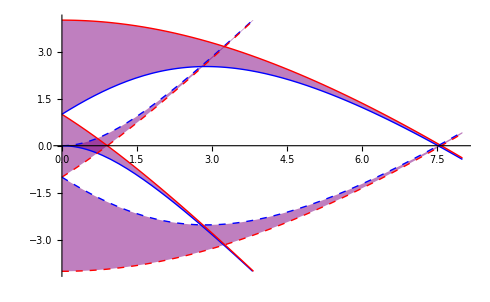

```mathematica
Plot[Flatten@Table[
{Tooltip[MathieuCharacteristicA[r,q],Subscript[ce,r]],Tooltip[MathieuCharacteristicB[r+1,q],Subscript[se,r+1]],Tooltip[-MathieuCharacteristicA[r,q],-Subscript[ce,r]],Tooltip[-MathieuCharacteristicB[r+1,q],-Subscript[se,r+1]]},{r,0,1}],{q,0,8},Evaluated->True,PlotRange->{All,{-4,4}},PlotStyle->{Directive[Thick,Blue],Directive[Thick,Red],Directive[Thick,Dashed,Blue],Directive[Thick,Dashed,Red]},Filling->Table[{2 n+1->{{2 n+2},Directive[Opacity[1/2],Purple]}},{n,0,3}]]
```